```mathematica
(*Funzione Legendre polinomiale associata*)
LGP[j_,m_,Θ_]:=Sqrt[(2 j+1)/(4π)((j-m)!)/((j+m)!)] LegendreP[j,m,Cos[Θ]]

(*Funzione f*)
fZZ[mm_,nn_,φ_]:=Re[If[0<φ<Pi/2||3*Pi/2<φ<2*Pi,Exp[I*(-mm+nn)*φ]/(2*Pi),-Exp[I*(-mm+nn)*φ]/(2*Pi)]]








nQubs=6;
jj=2^(nQubs-1);

(*Calcolo della matrice di integrali in theta*)
tttTheta=Table[Table[NIntegrate[LGP[jj,mm,θ]LGP[jj,nn,θ],{θ,0,π}],{mm,-jj,jj}],{nn,-jj,jj}];


tttTheta=tttTheta//Chop;

(*Plot della matrice con scala di colori*)
MatrixPlot[tttTheta,ColorFunction->"Rainbow",PlotLegends->BarLegend["Rainbow"]]

p = "done"
```

```mathematica
(*Calcolo della matrice di integrali in theta*)
tttPhi=Table[Table[NIntegrate[f[mm,nn,φ],{φ,0,2π}],{mm,-jj,jj}],{nn,-jj,jj}];

tttPhi=tttPhi//Chop;

MatrixPlot[tttPhi,ColorFunction->"Rainbow",PlotLegends->BarLegend["Rainbow"]]
```

```mathematica
(*Moltiplicazione elemento per elemento*)
tttProduct=tttTheta*tttPhi;

tttProduct=tttProduct//Chop;

MatrixPlot[tttProduct,ColorFunction->"Rainbow",PlotLegends->BarLegend["Rainbow"]]
```

```mathematica
(*Funzione f*)
fZZ[mm_,nn_,φ_]:=Re[If[0<φ<Pi/2||3*Pi/2<φ<2*Pi,Exp[I*(-mm+nn)*φ]/(2*Pi),-Exp[I*(-mm+nn)*φ]/(2*Pi)]]

nQubs=6;
jj=2^(nQubs-1);

tttPhi = Table[Table[NIntegrate[fZZ[mm,nn,φ],{φ,0,2π}],{mm,-jj,jj}],{nn, -jj,jj}];

MatrixPlot[tttPhi,ColorFunction->"Rainbow",PlotLegends->BarLegend["Rainbow"],FrameTicks->{Reverse[Table[{i,i-jj-1},{i,1,2*jj+1,4}]],(*Asse x (n) mantenuto come prima*)Reverse[Table[{i,i-jj-1},{i,1,2*jj+1,4}] ](*Asse y (m) modificato per ordinare da-j a j*)},FrameLabel->{"n","m"},FrameTicksStyle->Directive[FontSize->12], DataReversed->{True, False}]


(*Salvataggio del MatrixPlot e della legenda in un file PDF*)Export["MatrixPlotWithLegend.pdf",matrixPlot]
```

```mathematica
(*Funzione Legendre polinomiale associata*)
LGP[j_,m_,Θ_]:=Sqrt[(2 j+1)/(4π)((j-m)!)/((j+m)!)] LegendreP[j,m,Cos[Θ]]

(*Calcolo della matrice di integrali in theta*)
tttTheta=Table[Table[NIntegrate[LGP[jj,mm,θ]LGP[jj,nn,θ],{θ,0,π}],{mm,-jj,jj}],{nn,-jj,jj}];

tttTheta=tttTheta//Chop;

MatrixPlot[tttTheta,
ColorFunction->"Rainbow",
PlotLegends->BarLegend["Rainbow"],
FrameTicks->{Reverse[Table[{i,i-jj-1},{i,1,2*jj+1,4}]],Reverse[Table[{i,i-jj-1},{i,1,2*jj+1,4}] ]},
FrameLabel->{"n","m"},FrameTicksStyle->Directive[FontSize->12], DataReversed->{True, False}
]

(*Salvataggio del MatrixPlot e della legenda in un file PDF*)
Export["MatrixPlotWithLegend.pdf",matrixPlot]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.6996}. NIntegrate obtained -2.34188×10^-17 and 3.29655×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.6996}. NIntegrate obtained -1.21431×10^-17 and 3.20232×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.6996}. NIntegrate obtained 8.67362×10^-18 and 2.65749×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-Graphics-

MatrixPlotWithLegend.pdf

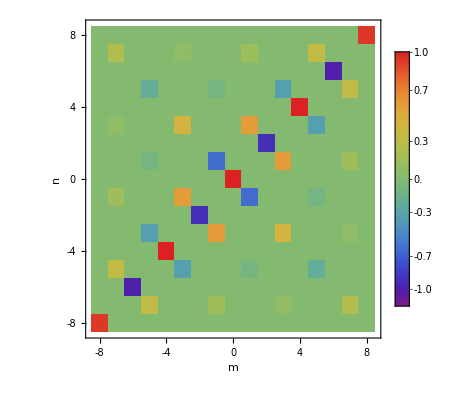

```mathematica
(*Funzione Legendre polinomiale associata*)
LGP[j_,m_,Θ_]:=Sqrt[(2 j+1)/(4π)((j-m)!)/((j+m)!)] LegendreP[j,m,Cos[Θ]]

(*φ integral when O=Subscript[Z, 1] Subscript[Z, 2]*)
IntZZ[m_, n_] := Module[{numerator,denominator, result},
If [m==n, result = 0,

(*otherwise, if m≠n*)
numerator = ⅈ (-1+ⅇ^(ⅈ (-m+n)π/2))^3 (1+ⅇ^(ⅈ (-m+n)π/2));
denominator = m-n;

result = numerator/denominator];

result // Chop
]

(*φ integral when O=Subscript[X, 1] Subscript[X, 2]*)
IntXX[m_,n_]:=Module[{numerator,denominator,result},
If[m==n,result=1/2 ⅇ^(-3/2 ⅈ m π) (1+ⅇ^(ⅈ m π)+ⅇ^(2 ⅈ m π)+ⅇ^(3 ⅈ m π)) π,

(*otherwise, if m≠n*)
result=-(ⅈ ⅇ^(-2 ⅈ m π) (ⅇ^((ⅈ m π)/2)-ⅇ^((ⅈ n π)/2)+ⅇ^(1/2 ⅈ (2 m+n) π)-ⅇ^(1/2 ⅈ (m+2 n) π)+ⅇ^(1/2 ⅈ (3 m+2 n) π)-ⅇ^(1/2 ⅈ (2 m+3 n) π)+ⅇ^(1/2 ⅈ (4 m+3 n) π)-ⅇ^(1/2 ⅈ (3 m+4 n) π)))/(m-n);
];

result // Chop
]


Integral[j_,m_,n_]:=Module[{integralPhi,integralTheta, result},
integralPhi=IntXX[m, n];

(*Check if integralPhi is zero. In this case is useless to calculate the integral in theta*)
If[integralPhi===0, 

integralTheta=0,
integralTheta=NIntegrate[LGP[j,m,θ]*LGP[j,n,θ]*Sin[θ],{θ,0,π}];

result = Chop[integralPhi*integralTheta]
] 
]

(*Study of the complete integrals*)
nQubs=4;
jj=2^(nQubs-1);

ttt = Table[Table[Integral[jj,mm, nn],{mm,-jj,jj}],{nn,-jj,jj}];

MatrixPlot[ttt,
ColorFunction->"Rainbow",
PlotLegends->BarLegend["Rainbow"],
FrameTicks->{Reverse[Table[{i,i-jj-1},{i,1,2*jj+1,4}]],Reverse[Table[{i,i-jj-1},{i,1,2*jj+1,4}] ]},
FrameLabel->{"n","m"},FrameTicksStyle->Directive[FontSize->12], DataReversed->{True, False}
]
```